#### Trajectory equation

```mathematica
x[η_,η0_,α_]:=α/(α-1)η(1-(η/η0)^(α-1))
(*x[η_,η0_,α_]:=α(η0-η+Log[η/η0])*)
```

#### Trajectory profile

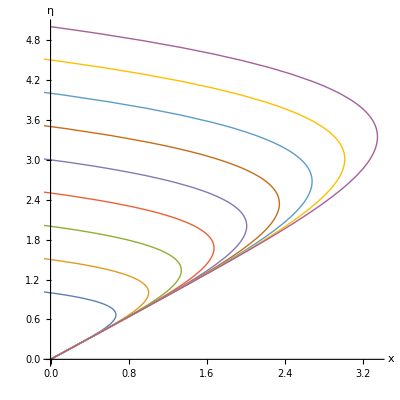

```mathematica
α=5;
η0m=5;
ParametricPlot[
Table[{x[η,η0,α],η},{η0,1,η0m,(η0m-1)/8}]//Evaluate,
{η,0,η0m},PlotRange->{{0,Automatic},All},
PlotStyle->Thick,
AxesLabel->{"x","η"},AxesStyle->Directive[FontSize->18],
GridLines->None]
(*,AspectRatio->2.2]*)
```

#### PDF

```mathematica
η0[η_,Δ_?NumericQ,α_?NumericQ]:=η0/.FindRoot[x[η,η0,α]==Δ,{η0,1}]//Re//Quiet
v[η_,η0_,α_?NumericQ]:=√((η-x[η,η0,α])^2+(η/α)^2)
p0[η0_,α_?NumericQ]:=√(α/(2π))Exp[-α/2 η0^2]
(* ρ is 2D PDF; pθ is marginalised over Δ *)
ρ[η_,η0_?NumericQ,α_?NumericQ]:=(α-1)/α(η0/η)^(α+1)Abs[1-(α+1)(η/η0)^α]/(√((1-(α+1)(η/η0)^α)^2+(α-1)^2))*v[η,η0,α]/v[η0,η0,α]*p0[η0,α]*HeavisideTheta[η-x[η,η0,α]]
```

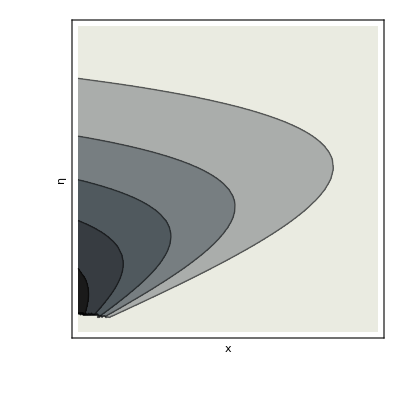

C:\Users\user\Dropbox\NYU\Grosberg\Code\Coloured_Noise\../../Documents/Paper_CN2/fig/GO/Separate/GO_PDF_L.pdf

```mathematica
α=5;
ρPlot=ContourPlot[ρ[η,η0[η,δ,α]//Evaluate,α],
{δ,0,0.4},{η,0,1},
PlotRange->Automatic,
ColorFunction->(ColorData["GrayTones",1-#1]&),
FrameLabel->{Style["x",Bold,FontSize->32],Style["η",Bold,FontSize->32]},
FrameTicks->None,
PlotLegends->None]
Export[NotebookDirectory[]<>"../../Documents/Paper_CN2/fig/GO/Separate/GO_PDF_L.pdf",%]
```

#### Spatial PDF

```mathematica
Manipulate[
Plot[ρ[η,η0[η,Δ,3],3]HeavisideTheta[η-Δ],{η,0,3.0},
PlotRange->{{0,3},{0,0.5}}],
{{Δ,0.1},0,0.5}]
```

#### Pressure

```mathematica
Manipulate[Max[0,δ*ρ[η,η0[η,δ,2],2]HeavisideTheta[η-δ]],{η,δ,3.0},{δ,0.001,1.0}]
```

```mathematica
For[y=2,y<21,y++,
NIntegrate[δ*ρ[η,η0[η,δ,y],y]HeavisideTheta[η-δ],{η,0,3.0},{δ,0.0,1.0},PrecisionGoal->4,AccuracyGoal->5]//Print
];
```

0.0165139

```mathematica
PLList=Table[NIntegrate[δ*ρ[η,η0[η,δ,y],y]HeavisideTheta[η-δ],{η,0,3.0},{δ,0.0,1.0},PrecisionGoal->4,AccuracyGoal->5],{y,2,20,1}]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
PLPlot=ListLogPlot[
PList,
PlotRange->{All,Automatic},
AxesLabel->{Style["α",Bold,FontSize->16],Style["P",Bold,FontSize->16]},
TicksStyle->14,
GridLines->Automatic,
PlotLegends->Automatic]
Export[NotebookDirectory[]<>"GO_PA_L.pdf",%]
```

$Aborted